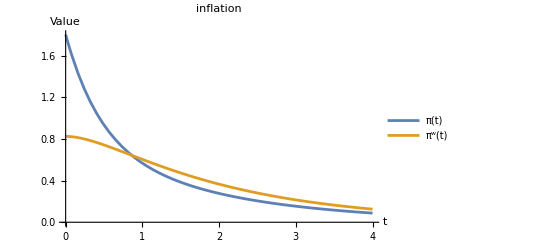

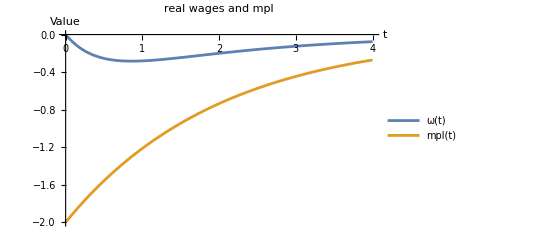

-Graphics-

```mathematica
ClearAll["Global`*"]


(* Under stated assumptions, it turns out to be essentially the same *)
(* Will upload derivations at some point, check GH *)
(* Once you add open economy, even keeping simple structure becomes complicated *)

rho=0.04;
lp=2*(2+rho);
lw=(1+rho);
Lambda=lp+lw;
(* 1/scale gives the (constant) expenditure share*)
scale = 3;
alpha=lp/(scale*Lambda);
(* fixed alpha, comes from single good case*)
falpha = alpha*scale; 
delta=0.5;
mpl0 = -2;
(* roots that solve x^2 - rho*x - Lambda s.t r1 < r2 *)
r1=-2.2428;
r2=2.2828;
 
(*Combining (24) and (25)*)
integrand1[s_,t_]:=(Lambda/(r2-r1))*(Exp[Min[r1*(t-s),r2*(t-s)]]-Exp[r1*t-r2*s])*(alpha*(mpl0*Exp[-delta*s]));

integrand2[tau_,t_]:=Exp[-r2*(tau-t)]*alpha*(mpl0*Exp[-delta*tau])

(*Giving us ω̇ OverDot[]*)
doto[t_]:=r1*NIntegrate[integrand1[s,t],{s,0,Infinity}]+Lambda*NIntegrate[integrand2[tau,t],{tau,t,Infinity}]

(*..to calculate inflation from p.16*)
pi[t_]:=Exp[-(rho+delta)*t]*(-lp*lw*mpl0)/(scale*Lambda*(rho+delta))-falpha*doto[t]
piw[t_]:=Exp[-(rho+delta)*t]*(-lp*lw*mpl0)/(scale*Lambda*(rho+delta))+(1-falpha)*doto[t]

omg[t_]:= NIntegrate[integrand1[s,t],{s,0,Infinity}]
mpl[t_] := mpl0*Exp[-delta*t]

Plot[{pi[t],piw[t]},{t,0,4},PlotLegends->{"π(t)","π^w(t)"},AxesLabel->{"t","Value"},PlotLabel->"inflation"]

Plot[{omg[t],mpl[t]},{t,0,4},PlotLegends->{"ω(t)","mpl(t)"},AxesLabel->{"t","Value"},PlotLabel->"real wages and mpl"]
```